```mathematica
Clear["Global`*"]
```

```mathematica
(* Mean frequencies of good cooperating individuals, gx *)
gxgood=(1-gx)*((1-ϵ)*g*HeavisideTheta[g-0.5]*HeavisideTheta[g-ϵ]+ϵ*(1-g)*HeavisideTheta[g-ϵ]*0.5);
gxbad=gx*((1-ϵ)*(1-g)*HeavisideTheta[1-g-ϵ]*HeavisideTheta[0.5-g]+ϵ*g*HeavisideTheta[1-g-ϵ]*0.5);
```

```mathematica
(* Mean frequencies of good defecting individuals, gy *)
gygood=(1-gy)*((1-ϵ)*(1-g)*HeavisideTheta[g-ϵ]*0.5+ϵ*g*HeavisideTheta[g-ϵ]*HeavisideTheta[g-0.5]);
gybad=gy*((1-ϵ)*g*HeavisideTheta[1-g-ϵ]*0.5+ϵ*(1-g)*HeavisideTheta[1-g-ϵ]*HeavisideTheta[0.5-g]);
```

```mathematica
(* Mean frequencies of good defecting individuals, gz *)
gzgood=(1-gz)*(1-ϵ)*((1-g)*HeavisideTheta[g-ϵ]*0.5+g*HeavisideTheta[g-ϵ]*HeavisideTheta[g-0.5]);
gzbad=gz*ϵ*((1-g)*HeavisideTheta[1-g-ϵ]*HeavisideTheta[0.5-g]+g*HeavisideTheta[1-g-ϵ]*0.5);
```

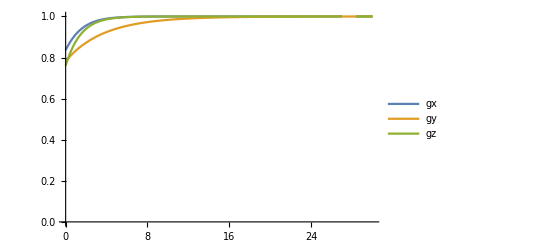

```mathematica
ϵ=0.25;
γ=1;
Δgx=gxgood-gxbad/.{gx->gx[t]};
Δgy=gygood-gybad/.{gy->gy[t]};
Δgz=gzgood-gzbad/.{gz->gz[t]};
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
r1=RandomReal[];
r2=RandomReal[];
r3=RandomReal[];
x=0.1;
y=0.7;
gx0=RandomReal[];
gy0=RandomReal[];
gz0=RandomReal[];
sol=NDSolve[{gx'[t]== γ*Δgx,gy'[t]==γ*Δgy,gz'[t]==γ*Δgz,gx[0]==gx0,gy[0]==gy0,gz[0]== gz0},{gx,gy,gz},{t,0,200}];
Plot[Evaluate[{gx[t],gy[t],gz[t]}/.sol],{t,0,30},PlotLegends->{"gx","gy","gz"},PlotRange->{0,1}]
```